### Estimation parameters

```mathematica
capN=10
m=3
```

10

3

```mathematica
6
```

6

### Recursion for the coefficients of the integer valued polynomials

```mathematica
q[0]:=1;
q[s_]:=Product[x-k,{k,1,s}]/Factorial[s];
```

```mathematica
q[0,0]:=1;
q[0,m_]:=0;
q[s_,k_]:=q[s-1,k-1]/s- q[s-1,k];
stirform[s_,k_]:=StirlingS1[s+1,k+1]/Factorial[s];
```

```mathematica
q[0,0]
stirform[0,0]
q[0,10]
stirform[0,10]
q[0,-1]
stirform[0,-1]
q[7,1]
stirform[7,1]
q[12,3]
stirform[12,3]
q[4,2]
Table[q[s,k],{s,0,5},{k,0,5}] //MatrixForm
Expand[q[0]]
Expand[q[1]]
Expand[q[2]]
Expand[q[3]]
Expand[q[4]]
Expand[q[5]]
```

1

1

0

0

0

«1 more identical outputs»

363/140

363/140

-5356117/1814400

-5356117/1814400

35/24

(1 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0
1 | -3/2 | 1/2 | 0 | 0 | 0
-1 | 11/6 | -1 | 1/6 | 0 | 0
1 | -25/12 | 35/24 | -5/12 | 1/24 | 0
-1 | 137/60 | -15/8 | 17/24 | -1/8 | 1/120)

1

-1+x

1-(3 x)/2+x^2/2

-1+(11 x)/6-x^2+x^3/6

1-(25 x)/12+(35 x^2)/24-(5 x^3)/12+x^4/24

-1+(137 x)/60-(15 x^2)/8+(17 x^3)/24-x^4/8+x^5/120

```mathematica
stirform[0,10]
```

0

### Coefficient of the discrete orthogonal polynomials

```mathematica
d[k_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s],{s,0,k}]
P[k_,i_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s,i],{s,0,k}];
```

```mathematica
Table[P[k,i],{k,0,5},{i,0,5}] //MatrixForm
Expand[d[0]]
Expand[d[1]]
Expand[d[2]]
Expand[d[3]]
Expand[d[4]]
Expand[d[5]]
```

(1 | 0 | 0 | 0 | 0 | 0
-11 | 2 | 0 | 0 | 0 | 0
66 | -33 | 3 | 0 | 0 | 0
-286 | 761/3 | -55 | 10/3 | 0 | 0
1001 | -3850/3 | 5635/12 | -385/6 | 35/12 | 0
-3003 | 24752/5 | -10395/4 | 581 | -231/4 | 21/10)

1

-11+2 x

66-33 x+3 x^2

-286+(761 x)/3-55 x^2+(10 x^3)/3

1001-(3850 x)/3+(5635 x^2)/12-(385 x^3)/6+(35 x^4)/12

-3003+(24752 x)/5-(10395 x^2)/4+581 x^3-(231 x^4)/4+(21 x^5)/10

### Cramer-Rao bounds

```mathematica
CRB[i_,snr_]:=Sum[P[k,i]^2/Binomial[capN+k,2*k+1]/Binomial[2*k,k],{k,0,m}]/(2*snr);
ApproxCRB[i_,snr_]:=1/(2*capN^(2*i+1)*snr)*(1/(2*i+1)+(m+1)^2/(2*capN*(i+1)^2)-1/(2*capN))*((m+i+1)*Binomial[m+i,i]*Binomial[m,i])^2;
```

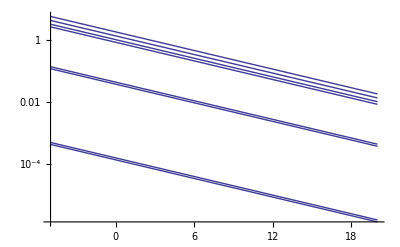

```mathematica
LogPlot[Flatten[Table[{CRB[i,10^(snrdb/10)],ApproxCRB[i,10^(snrdb/10)]},{i,0,m}]],{snrdb,-5,20}]
```

```mathematica
Table[{CRB[2,10^(snrdb/10)],ApproxCRB[2,10^(snrdb/10)]},{snrdb,-5,20}]
```

{{(103 √(5/2))/1144,387/(1000 √10)},{(103 5^(2/5))/(1144 2^(3/5)),387/(1000 10^(3/5))},{(103 5^(3/10))/(1144 2^(7/10)),387/(1000 10^(7/10))},{(103 5^(1/5))/(1144 2^(4/5)),387/(1000 10^(4/5))},{(103 5^(1/10))/(1144 2^(9/10)),387/(1000 10^(9/10))},{103/2288,387/10000},{103/(2288 10^(1/10)),387/(10000 10^(1/10))},{103/(2288 10^(1/5)),387/(10000 10^(1/5))},{103/(2288 10^(3/10)),387/(10000 10^(3/10))},{103/(2288 10^(2/5)),387/(10000 10^(2/5))},{103/(2288 √10),387/(10000 √10)},{103/(2288 10^(3/5)),387/(10000 10^(3/5))},{103/(2288 10^(7/10)),387/(10000 10^(7/10))},{103/(2288 10^(4/5)),387/(10000 10^(4/5))},{103/(2288 10^(9/10)),387/(10000 10^(9/10))},{103/22880,387/100000},{103/(22880 10^(1/10)),387/(100000 10^(1/10))},{103/(22880 10^(1/5)),387/(100000 10^(1/5))},{103/(22880 10^(3/10)),387/(100000 10^(3/10))},{103/(22880 10^(2/5)),387/(100000 10^(2/5))},{103/(22880 √10),387/(100000 √10)},{103/(22880 10^(3/5)),387/(100000 10^(3/5))},{103/(22880 10^(7/10)),387/(100000 10^(7/10))},{103/(22880 10^(4/5)),387/(100000 10^(4/5))},{103/(22880 10^(9/10)),387/(100000 10^(9/10))},{103/228800,387/1000000}}

Plot the CRBs to a file

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/crbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[CRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/crbN10m3i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/crbN10m3i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/crbN10m3i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[ApproxCRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN10m3i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN10m3i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN10m3i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

```mathematica
FullSimplify[Factorial[s+k]/Factorial[s]/Factorial[k]*Factorial[n-s-1]/Factorial[n-k-1]/Factorial[n-k+s]*Binomial[l+k,l]*Binomial[n-l-1,N-k-1]/Binomial[2*k,k]/Binomial[n+k,2*k+1]]
```

((1+2 k) Binomial[k+l,l] Binomial[-1-l+n,-1-k+N] (k+s)! Gamma[1+k] Gamma[n-s])/(Gamma[1+k+n] Gamma[1+s] Gamma[1-k+n+s])

```mathematica
FullSimplify[Binomial[n-s-1,n-k-1]/Binomial[n+k,2*k+1]]
```

Binomial[-1+n-s,-1-k+n]/Binomial[k+n,1+2 k]

```mathematica
Binomial[11,3]
```

165

```mathematica
P[4,1]
```

-3850/3